```mathematica
(*
"How lights are reflected on a lens";
*)
```

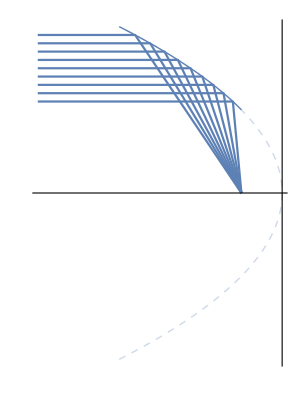

```mathematica
Show[{ParametricPlot[{-t^2,t},{t,.5,1},Axes->{True,False},AxesOrigin->{0,0},PlotStyle->Thick,Ticks->None,PlotRange->All],ParametricPlot[{-t^2,t},{t,-1,1},Axes->{True,False},AxesOrigin->{0,0},PlotStyle->Directive[Thick,Opacity[.3],Dashed],Ticks->None],ListLinePlot[{{-1.5,#},{-#^2,#},{-1/4,0}}]&/@Range[.55,.95,.05]}]
```